```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
data=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\lowT.dat",Real];
data=ArrayReshape[data,{Length[data]/5,5}];
data={data[[;;,1;;4]],data[[;;,5]]}//Transpose;
```

```mathematica
Tmin=30;
f=Interpolation[data,InterpolationOrder->4];
g[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS]Log[2,Max[T,10^-3]/Tmin+1],T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
p[T_,μB_,μQ_,μS_]:=T^4 g[T,μB,μQ,μS];
s[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T]];
ρB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB]];
ρQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ]];
ρS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μS]];
e[T_,μB_,μQ_,μS_]:=T s[T,μB,μQ,μS]+μB ρB[T,μB,μQ,μS]+μQ ρQ[T,μB,μQ,μS]+μS ρS[T,μB,μQ,μS]-p[T,μB,μQ,μS];
χTT[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,T]];
χTμB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μB]];
χTμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μQ]];
χTμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μS]];
χμBμB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μB]];
χμBμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μQ]];
χμBμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μS]];
χμQμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ,μQ]];
χμQμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ,μS]];
χμSμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μS,μS]];
χ[T_,μB_,μQ_,μS_]:={{χTT[T,μB,μQ,μS],χTμB[T,μB,μQ,μS],χTμQ[T,μB,μQ,μS],χTμS[T,μB,μQ,μS]},{χTμB[T,μB,μQ,μS],χμBμB[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS]},{χTμQ[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμQμQ[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS]},{χTμS[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS],χμSμS[T,μB,μQ,μS]}};
χp[T_,μB_,μQ_,μS_]:=χ[T,μB,μQ,μS]*{T,μB,μQ,μS};
cs2[T_,μB_,μQ_,μS_]:=Module[{dT,dμB,dμQ,dμS,solϵ,solB,solQ,solS,term1,term2,term3,term4},
solϵ=Solve[#==0&/@(χ[T,μB,μQ,μS][[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten;
solB=Solve[{Total[χp[T,μB,μQ,μS].{dT,dμB,dμQ,dμS}]==0,(χ[T,μB,μQ,μS][[3]].{dT,dμB,dμQ,dμS})==0,(χ[T,μB,μQ,μS][[4]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
solQ=Solve[{Total[χp[T,μB,μQ,μS].{dT,dμB,dμQ,dμS}]==0,(χ[T,μB,μQ,μS][[2]].{dT,dμB,dμQ,dμS})==0,(χ[T,μB,μQ,μS][[4]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
solS=Solve[{Total[χp[T,μB,μQ,μS].{dT,dμB,dμQ,dμS}]==0,(χ[T,μB,μQ,μS][[2]].{dT,dμB,dμQ,dμS})==0,(χ[T,μB,μQ,μS][[3]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
term1=(dT s[T,μB,μQ,μS]+dμB ρB[T,μB,μQ,μS]+dμQ ρQ[T,μB,μQ,μS]+dμS ρS[T,μB,μQ,μS]/.solϵ)/Total[χp[T,μB,μQ,μS].{dT,dμB,dμQ,dμS}/.solϵ]//FullSimplify;term2=(ρB[T,μB,μQ,μS]/(e[T,μB,μQ,μS]+p[T,μB,μQ,μS]))(dT s[T,μB,μQ,μS]+dμB ρB[T,μB,μQ,μS]+dμQ ρQ[T,μB,μQ,μS]+dμS ρS[T,μB,μQ,μS]/.solB)/((χ[T,μB,μQ,μS][[2]].{dT,dμB,dμQ,dμS})/.solB)//FullSimplify;term3=(ρQ[T,μB,μQ,μS]/(e[T,μB,μQ,μS]+p[T,μB,μQ,μS]))(dT s[T,μB,μQ,μS]+dμB ρB[T,μB,μQ,μS]+dμQ ρQ[T,μB,μQ,μS]+dμS ρS[T,μB,μQ,μS]/.solQ)/((χ[T,μB,μQ,μS][[3]].{dT,dμB,dμQ,dμS})/.solQ)//FullSimplify;term4=(ρS[T,μB,μQ,μS]/(e[T,μB,μQ,μS]+p[T,μB,μQ,μS]))(dT s[T,μB,μQ,μS]+dμB ρB[T,μB,μQ,μS]+dμQ ρQ[T,μB,μQ,μS]+dμS ρS[T,μB,μQ,μS]/.solS)/((χ[T,μB,μQ,μS][[4]].{dT,dμB,dμQ,dμS})/.solS)//FullSimplify;
(*{solϵ,solB,solQ,solS,term1,term2,term3,term4,term1+term2+term3+term4}*)
term1+term2+term3+term4
];
```

```mathematica
cs2[35,50,50,50]
```

0.194288

```mathematica
Table[{T,μB,μQ,μS,T^-4 p[T,μB,μQ,μS],T^-3 s[T,μB,μQ,μS],T^-3 ρB[T,μB,μQ,μS],T^-3 ρS[T,μB,μQ,μS],T^-3 ρQ[T,μB,μQ,μS],T^-4 e[T,μB,μQ,μS],cs2[T,μB,μQ,μS]},{T,35,35,5},{μB,50,50,5},{μQ,50,50,5},{μS,50,50,5}]
35^-2{χμBμB[T,μB,μQ,μS],χμQμQ[T,μB,μQ,μS],χμSμS[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS],χTμB[T,μB,μQ,μS],χTμQ[T,μB,μQ,μS],χTμS[T,μB,μQ,μS],χTT[T,μB,μQ,μS]}/.{T->35,μB->50,μQ->50,μS->50}
```

{{{{{35,50,50,50,0.0778649,0.435571,-0.0000106753,0.000180324,0.0552029,0.43681,0.194288}}}}}

{0.0000309408,0.0586347,0.00013684,0.0000186726,-0.0000278201,0.0000548779,-0.000222964,0.2376,0.00175421,1.90444}

```mathematica
30^-2 χ[30,50,50,50]//MatrixForm
```

(1.90444 | -0.000222964 | 0.2376 | 0.00175421
-0.000222964 | 0.0000309408 | 0.0000186726 | -0.0000278201
0.2376 | 0.0000186726 | 0.0586347 | 0.0000548779
0.00175421 | -0.0000278201 | 0.0000548779 | 0.00013684)

```mathematica
sol=Solve[#==0&/@(35^2 χ[35,50,50,50][[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten
```

{dμB→-0.518852 dT,dμQ→-4.04147 dT,dμS→-11.3041 dT}

```mathematica
(dT s[35,50,50,50]+dμB ρB[35,50,50,50]+dμQ ρQ[35,50,50,50]+dμS ρS[35,50,50,50]/.sol)/Total[35^2 χp[35,50,50,50].{dT,dμB,dμQ,dμS}/.sol]//FullSimplify
```

0.000185821

```mathematica
Table[Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}].{dT,dμB,dμQ,dμS}//MatrixForm
```

(dT χ_(T,T)+dμB χ_(T,μB)+dμQ χ_(T,μQ)+dμS χ_(T,μS)
dT χ_(μB,T)+dμB χ_(μB,μB)+dμQ χ_(μB,μQ)+dμS χ_(μB,μS)
dT χ_(μQ,T)+dμB χ_(μQ,μB)+dμQ χ_(μQ,μQ)+dμS χ_(μQ,μS)
dT χ_(μS,T)+dμB χ_(μS,μB)+dμQ χ_(μS,μQ)+dμS χ_(μS,μS))

```mathematica
sol=Solve[(Table[Subscript[χ, a,b],{a,{T,μB}},{b,{T,μB}}][[2]].{dT,dμB})==0,dμB]//First
dpdϵ==(dT s+dμB ρB/.sol)/Total[(Table[a Subscript[χ, a,b],{a,{T,μB}},{b,{T,μB}}].{dT,dμB})/.sol]//FullSimplify
```

{dμB→-(dT χ_(μB,T))/(χ_(μB,μB))}

dpdϵ==(ρB χ_(μB,T)-s χ_(μB,μB))/(T χ_(T,μB) χ_(μB,T)-T χ_(T,T) χ_(μB,μB))

```mathematica
sol2=Solve[#==0&/@(Table[Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}][[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten//FullSimplify
dpdϵ==(dT s+dμB ρB+dμQ ρQ+dμS ρS/.sol2)/Total[(Table[a Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}].{dT,dμB,dμQ,dμS})/.sol2]//FullSimplify
```

{dμB→(dT (χ_(μB,μS) (χ_(μQ,μQ) χ_(μS,T)-χ_(μQ,T) χ_(μS,μQ))+χ_(μB,μQ) (-χ_(μQ,μS) χ_(μS,T)+χ_(μQ,T) χ_(μS,μS))+χ_(μB,T) (χ_(μQ,μS) χ_(μS,μQ)-χ_(μQ,μQ) χ_(μS,μS))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS))),dμQ→(dT (χ_(μB,μS) (-χ_(μQ,μB) χ_(μS,T)+χ_(μQ,T) χ_(μS,μB))+χ_(μB,μB) (χ_(μQ,μS) χ_(μS,T)-χ_(μQ,T) χ_(μS,μS))+χ_(μB,T) (-χ_(μQ,μS) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μS))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS))),dμS→(dT (χ_(μB,μQ) (χ_(μQ,μB) χ_(μS,T)-χ_(μQ,T) χ_(μS,μB))+χ_(μB,μB) (-χ_(μQ,μQ) χ_(μS,T)+χ_(μQ,T) χ_(μS,μQ))+χ_(μB,T) (χ_(μQ,μQ) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μQ))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS)))}

dpdϵ==(-ρS χ_(μB,μB) χ_(μQ,μQ) χ_(μS,T)+ρQ χ_(μB,μB) χ_(μQ,μS) χ_(μS,T)+ρS χ_(μB,T) χ_(μQ,μQ) χ_(μS,μB)-ρQ χ_(μB,T) χ_(μQ,μS) χ_(μS,μB)+ρS χ_(μB,μB) χ_(μQ,T) χ_(μS,μQ)-ρS χ_(μB,T) χ_(μQ,μB) χ_(μS,μQ)+ρB χ_(μB,T) χ_(μQ,μS) χ_(μS,μQ)-s χ_(μB,μB) χ_(μQ,μS) χ_(μS,μQ)+χ_(μB,μS) (χ_(μQ,μQ) (ρB χ_(μS,T)-s χ_(μS,μB))+χ_(μQ,μB) (-ρQ χ_(μS,T)+s χ_(μS,μQ))+χ_(μQ,T) (ρQ χ_(μS,μB)-ρB χ_(μS,μQ)))+(χ_(μB,μB) (-ρQ χ_(μQ,T)+s χ_(μQ,μQ))+χ_(μB,T) (ρQ χ_(μQ,μB)-ρB χ_(μQ,μQ))) χ_(μS,μS)+χ_(μB,μQ) (χ_(μQ,μS) (-ρB χ_(μS,T)+s χ_(μS,μB))+χ_(μQ,μB) (ρS χ_(μS,T)-s χ_(μS,μS))+χ_(μQ,T) (-ρS χ_(μS,μB)+ρB χ_(μS,μS))))/(T (χ_(T,μB) χ_(μB,μS) χ_(μQ,μQ) χ_(μS,T)-χ_(T,μB) χ_(μB,μQ) χ_(μQ,μS) χ_(μS,T)-χ_(T,T) χ_(μB,μS) χ_(μQ,μQ) χ_(μS,μB)+χ_(T,T) χ_(μB,μQ) χ_(μQ,μS) χ_(μS,μB)-χ_(T,μB) χ_(μB,μS) χ_(μQ,T) χ_(μS,μQ)+χ_(T,T) χ_(μB,μS) χ_(μQ,μB) χ_(μS,μQ)+χ_(T,μB) χ_(μB,T) χ_(μQ,μS) χ_(μS,μQ)-χ_(T,T) χ_(μB,μB) χ_(μQ,μS) χ_(μS,μQ)+χ_(T,μS) (χ_(μQ,μQ) (-χ_(μB,μB) χ_(μS,T)+χ_(μB,T) χ_(μS,μB))+χ_(μB,μQ) (χ_(μQ,μB) χ_(μS,T)-χ_(μQ,T) χ_(μS,μB))+(χ_(μB,μB) χ_(μQ,T)-χ_(μB,T) χ_(μQ,μB)) χ_(μS,μQ))+(χ_(T,μB) (χ_(μB,μQ) χ_(μQ,T)-χ_(μB,T) χ_(μQ,μQ))+χ_(T,T) (-χ_(μB,μQ) χ_(μQ,μB)+χ_(μB,μB) χ_(μQ,μQ))) χ_(μS,μS)+χ_(T,μQ) (χ_(μQ,μS) (χ_(μB,μB) χ_(μS,T)-χ_(μB,T) χ_(μS,μB))+χ_(μB,μS) (-χ_(μQ,μB) χ_(μS,T)+χ_(μQ,T) χ_(μS,μB))+(-χ_(μB,μB) χ_(μQ,T)+χ_(μB,T) χ_(μQ,μB)) χ_(μS,μS))))

```mathematica
35^-2 χ[35,50,50,50]//Flatten//DeleteDuplicates
```

{1.90444,-0.000222964,0.2376,0.00175421,0.0000309408,0.0000186726,-0.0000278201,0.0586347,0.0000548779,0.00013684}

```mathematica
fp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T]];
fpp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T,T]];
g2[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS]Exp[a1 (1-(Tmin/T)^2)]//.{a1->(-2 a2 f0+15 fp0)/f0,f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
```

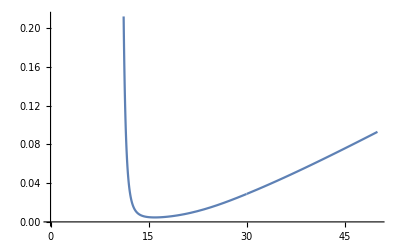

```mathematica
Plot[g2[T,0,0,0],{T,0,50}]
```

General::munfl: Exp[-2.39621×10^9] is too small to represent as a normalized machine number; precision may be lost.

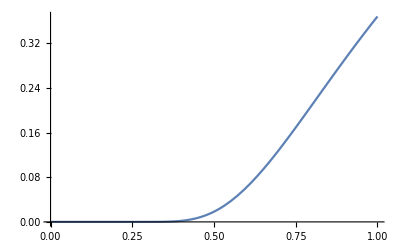

```mathematica
Exp[a (1-(T0/T)^2)]
```

```mathematica
D[f0 Exp[a1 (1-(Tmin/T)^2)],{T,0}]/.T->Tmin
Solve[fp0==D[f0 Exp[a1 (1-(Tmin/T)^2)+a2 (1-(Tmin/T)^4)],{T,1}]/.T->Tmin,a1]
```

f0

{{a1→(-2 a2 f0+15 fp0)/f0}}